# Happy Numbers

```mathematica
Get["/home/blmayer/repos/thesis/visibility.mx"]
```

```mathematica
Get[NotebookDirectory[]<>"happy-numbers.mx"]
```

```mathematica
numbers=happies[[;;30000]];
```

```mathematica
Select[series,EvenQ@#[[2]]&]//Length
```

29928

```mathematica
Cases[PrimeQ/@numbers,True]//Length
```

2799

```mathematica
series=Table[{x,Length@Divisors[x]},{x,numbers}]
```

{{1,1},{7,2},{10,4},{13,2},{19,2},{23,2},{28,6},{31,2},{32,6},{44,6},{49,3},{68,6},{70,8},{79,2},{82,4},{86,4},{91,4},{94,4},{97,2},{100,9},{103,2},{109,2},{129,4},{130,8},{133,4},{139,2},{167,2},{176,10},29944,{204355,8},{204357,8},{204368,20},{204371,2},{204372,36},{204374,8},{204375,20},{204381,6},{204382,4},{204384,24},{204386,16},{204408,48},{204417,16},{204422,8},{204423,4},{204432,20},{204435,48},{204437,2},{204438,16},{204444,30},{204449,4},{204453,6},{204455,8},{204456,32},{204465,16},{204471,8},{204473,4},{204480,84}}
 |  |  |  |

```mathematica
Max[series[[All,2]]]
```

160

```mathematica
series=Table[{x,orbit[x]},{x,numbers}]
```

{{1,0},{7,1},{10,3},{13,1},{19,1},{23,1},{28,4},{31,1},{32,4},{44,4},{49,2},{68,4},{70,4},{79,1},{82,3},{86,3},{91,3},{94,3},{97,1},{100,3},{103,1},{109,1},{129,3},{130,4},{133,3},{139,1},{167,1},{176,4},{188,4},29942,{204354,5},{204355,4},{204357,4},{204368,5},{204371,1},{204372,4},{204374,4},{204375,5},{204381,4},{204382,3},{204384,5},{204386,3},{204408,5},{204417,3},{204422,4},{204423,3},{204432,5},{204435,5},{204437,1},{204438,3},{204444,5},{204449,3},{204453,4},{204455,4},{204456,5},{204465,3},{204471,4},{204473,3},{204480,6}}
 |  |  |  |

```mathematica
Max[series[[All,2]]]
```

6

```mathematica
Select[series,EvenQ@#[[2]]&]//Length
```

9234

```mathematica
orbit[x_]:=Block[{d=0,n=x},
While[n>2,n=Length@Divisors[n];d+=1;];
Return[d]
]
```

## Divisors

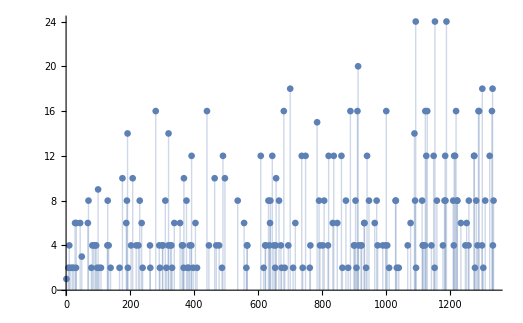

```mathematica
ListPlot[series[[;;200]],Filling->Axis]
```

### Evolution of SDL complexity

```mathematica
sdl[vals_List]:=Block[{counts,Hmax,H,delta},
counts=Counts[#]/Length@vals&@vals;
Hmax=Log[Length@counts];
H=-Total[# Log[#]&/@counts]//N;
delta=H/Hmax;
{4 delta(1-delta),delta}//N
]
```

```mathematica
series
```

{{1,1},{7,2},{10,4},{13,2},{19,2},{23,2},{28,6},{31,2},{32,6},{44,6},{49,3},{68,6},{70,8},{79,2},{82,4},{86,4},{91,4},{94,4},{97,2},{100,9},{103,2},{109,2},{129,4},{130,8},{133,4},{139,2},{167,2},{176,10},19944,{135318,16},{135321,8},{135327,8},{135329,2},{135347,2},{135351,12},{135355,16},{135358,4},{135367,2},{135371,4},{135372,24},{135374,8},{135376,10},{135381,4},{135385,4},{135392,12},{135407,8},{135414,12},{135419,4},{135426,8},{135437,4},{135441,12},{135446,4},{135462,16},{135464,32},{135470,32},{135473,8},{135491,4}}
 |  |  |  |

```mathematica
sdl[series[[All,2]]]
```

{0.977644,0.57476}

```mathematica
sdls=Table[sdl[series[[;;x,2]]][[2]],{x,Length@series}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

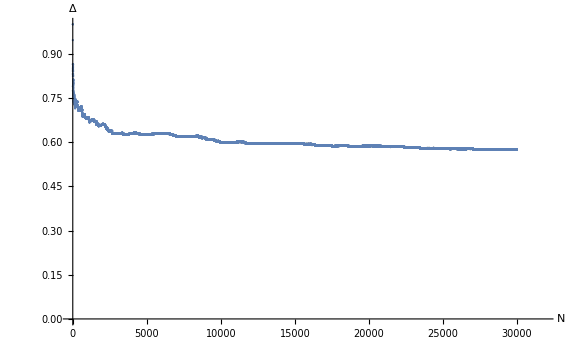

```mathematica
ListPlot[sdls,AxesLabel-> {Style["N",36, Italic],Style["Δ", 36,Italic]},LabelStyle->20,ImageSize->Large,PlotRange->{{0,31800},{0,1}}]
```

## Visibility graphs

## Natural Visibility

```mathematica
happyNVLinks=naturalVisibility[series];
```

```mathematica
happyNVGraph=Graph[happyNVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

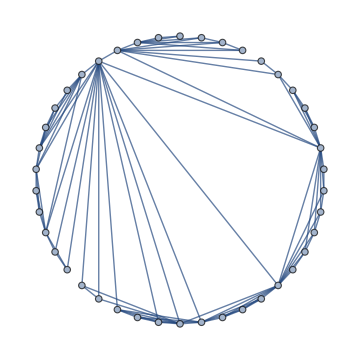

```mathematica
Graph[happyNVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding",ImageSize->Medium]
```

```mathematica
happyNVDegrees=Counts[VertexDegree[happyNVGraph]]/Length@VertexDegree[happyNVGraph]
```

<|2→1819/15000,6→487/5000,3→1623/10000,4→1663/10000,8→253/5000,12→1/60,15→91/10000,9→43/1250,5→1021/7500,7→673/10000,19→149/30000,16→241/30000,11→659/30000,24→1/400,23→7/2500,46→1/2500,10→69/2500,13→17/1250,14→59/5000,17→199/30000,18→187/30000,30→13/10000,35→29/30000,28→11/6000,29→29/30000,63→1/15000,26→1/625,27→13/7500,33→7/7500,22→49/15000,20→23/6000,25→9/5000,21→109/30000,39→3/5000,31→31/30000,32→13/15000,41→1/2500,57→1/5000,77→1/15000,42→1/2000,43→1/2500,54→1/5000,56→1/10000,37→7/10000,36→17/30000,76→1/15000,112→1/30000,34→7/7500,40→1/2500,38→1/2000,51→11/30000,44→1/5000,59→1/10000,60→1/10000,52→1/10000,45→1/3750,65→1/10000,80→1/30000,58→1/30000,72→1/30000,104→1/30000,53→1/6000,48→1/7500,49→1/6000,50→1/10000,55→1/15000,75→1/30000,99→1/30000,74→1/30000,107→1/30000,47→1/6000,66→1/30000,68→1/30000,69→1/30000,61→1/30000,91→1/30000,73→1/30000|>

```mathematica
happyNVDegrees[1]=.
```

```mathematica
data=Table[{x,happyNVDegrees[x]},{x,Keys[happyNVDegrees]}];
happyNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.0996976 ⅇ^(-0.664207 k) k^2.24978]

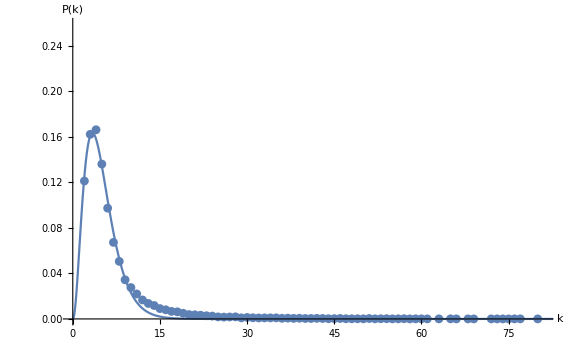

```mathematica
happyNVPlot=Show[
ListPlot[happyNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[happyNVNlm[x],{x,0,Max[Keys[happyNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -2.24978 | 0.0988495 | {-2.44675,-2.05282}
c | 0.0996976 | 0.00472034 | {0.0902921,0.109103}
d | 0.664207 | 0.0231207 | {0.618138,0.710277}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[happyNVGraph]//N,MeanGraphDistance[happyNVGraph]//N,
GlobalClusteringCoefficient[happyNVGraph]//N,Mean[happyNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 6.60953 | 7.39084 | 0.349324 | 9.56797×10^-6 | -2.24978 ± 0.196962 | 0.0996976 ± 0.00940549 | 0.664207 ± 0.046069

## Horizontal Visibility

```mathematica
happyHVLinks=horizontalVisibility[series];
```

```mathematica
happyHVGraph=Graph[happyHVLinks,DirectedEdges->False,VertexLabels->"Name",GraphLayout->"CircularEmbedding"];
```

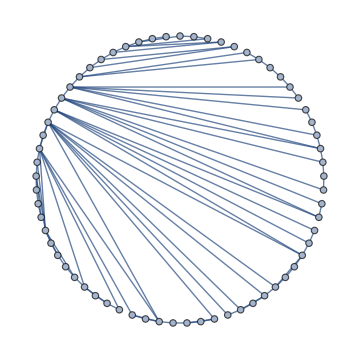

```mathematica
Graph[happyHVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding",ImageSize->Medium]
```

```mathematica
happyHVDegrees=Counts[VertexDegree[happyHVGraph]]/Length@VertexDegree[happyHVGraph]
```

<|1→1/30000,2→3169/7500,3→3269/15000,4→1061/7500,7→157/5000,6→99/2000,5→253/3000,10→239/30000,8→49/2500,9→33/2500,12→13/5000,11→151/30000,13→19/10000,14→1/1200,15→7/10000,16→7/15000,17→1/3000,19→1/10000,20→1/30000,23→1/30000|>

```mathematica
happyHVDegrees[1]=.
```

```mathematica
data=Table[{x,happyHVDegrees[x]},{x,Keys[happyHVDegrees]}];
happyHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[(1.33806 ⅇ^(-0.330865 k))/k^0.713816]

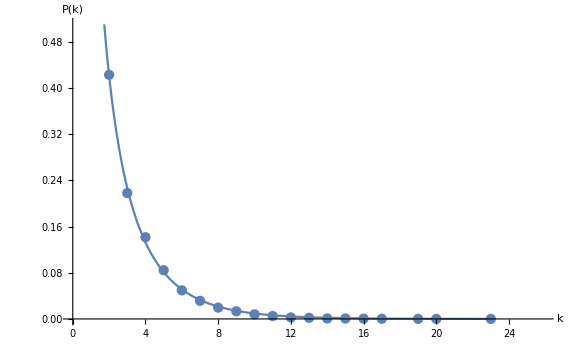

```mathematica
happyHVPlot=Show[
ListPlot[happyHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[happyHVNlm[x],{x,0,Max[Keys[happyHVDegrees]]},PlotRange->{{0,25},{0,0.51}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | 0.713816 | 0.108494 | {0.483818,0.943814}
c | 1.33806 | 0.0306063 | {1.27317,1.40294}
d | 0.330865 | 0.033378 | {0.260107,0.401623}

```mathematica
TableForm[
Flatten[{"horizontal visibility",Mean@ VertexDegree[happyHVGraph]//N,MeanGraphDistance[happyHVGraph]//N,
GlobalClusteringCoefficient[happyHVGraph]//N,Mean[happyHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"},None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 3.5084 | 15.4267 | 0.271018 | 9.76565×10^-6 | 0.713816 ± 0.229998 | 1.33806 ± 0.0648825 | 0.330865 ± 0.0707582

## Orbits

```mathematica
orbits=Table[{x,orbit[x]},{x,numbers}];
```

```mathematica
sdl[orbits[[All,2]]]
```

{0.853102,0.691636}

```mathematica
orbitsSDLs=Table[sdl[orbits[[;;x,2]]][[2]],{x,Length@orbits}];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

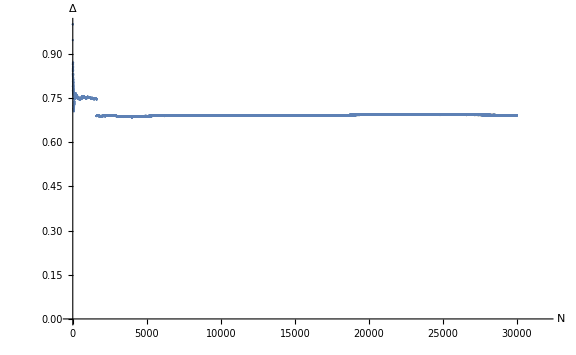

```mathematica
ListPlot[orbitsSDLs,AxesLabel-> {Style["N",36, Italic],Style["Δ", 36,Italic]},LabelStyle->20,ImageSize->Large,PlotRange->{{0,31800},{0,1}}]
```

## Visibility graphs

## Natural Visibility

```mathematica
happyOrbitsNVLinks=naturalVisibility[orbits];
```

```mathematica
happyOrbitsNVGraph=Graph[happyOrbitsNVLinks,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

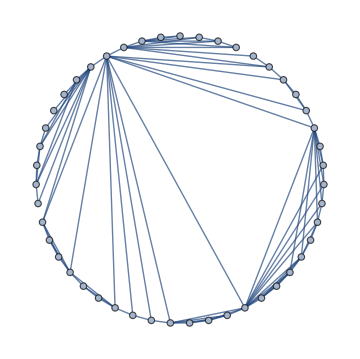

```mathematica
Graph[happyOrbitsNVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding",ImageSize->Medium]
```

```mathematica
happyOrbitsNVDegrees=Counts[VertexDegree[happyOrbitsNVGraph]]/Length@VertexDegree[happyOrbitsNVGraph]//KeySort
```

<|2→2663/15000,3→3239/15000,4→3/16,5→627/5000,6→479/6000,7→583/10000,8→1333/30000,9→479/15000,10→43/1875,11→247/15000,12→343/30000,13→41/6000,14→47/10000,15→2/625,16→11/6000,17→23/15000,18→3/5000,19→1/1875,20→7/30000,21→7/30000,22→1/6000,23→1/10000,24→1/5000,25→1/3750,26→7/30000,27→1/6000,28→1/15000,29→1/10000,30→1/5000,31→1/10000,32→7/30000,33→1/5000,34→1/15000,35→1/10000,36→7/30000,37→1/7500,38→1/10000,39→1/30000,40→1/5000,41→1/10000,42→1/7500,43→1/15000,44→1/30000,45→1/7500,46→1/15000,47→1/10000,48→1/10000,49→1/6000,50→1/10000,51→1/10000,52→1/10000,53→1/10000,54→1/30000,55→1/7500,56→1/7500,57→1/15000,58→1/10000,59→1/6000,60→1/30000,61→1/15000,62→1/30000,63→1/10000,64→1/15000,65→1/15000,66→1/30000,67→1/30000,68→1/6000,69→1/10000,70→1/30000,71→1/15000,72→1/15000,73→1/15000,74→1/30000,75→1/15000,76→1/30000,77→1/10000,78→1/15000,79→1/15000,80→1/10000,81→1/7500,82→1/10000,83→1/30000,84→1/30000,85→1/7500,87→1/15000,88→1/30000,89→1/10000,90→1/10000,91→1/10000,93→1/30000,94→1/30000,95→1/10000,96→1/10000,97→1/30000,99→1/30000,102→1/15000,103→1/10000,104→1/15000,105→1/30000,106→1/30000,108→1/15000,109→1/30000,110→1/30000,111→1/30000,112→1/30000,119→1/30000,120→1/15000,123→1/30000,131→1/30000,134→1/30000,135→1/30000,136→1/30000,140→1/30000,141→1/30000,154→1/30000,161→1/30000,164→1/15000,180→1/30000,183→1/30000,192→1/30000,235→1/30000,246→1/30000,517→1/30000,785→1/30000|>

```mathematica
happyOrbitsNVDegrees[1]=.
```

```mathematica
data=Table[{x,happyOrbitsNVDegrees[x]},{x,Keys[happyOrbitsNVDegrees]}];
happyOrbitsNVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[0.188599 ⅇ^(-0.771262 k) k^2.19055]

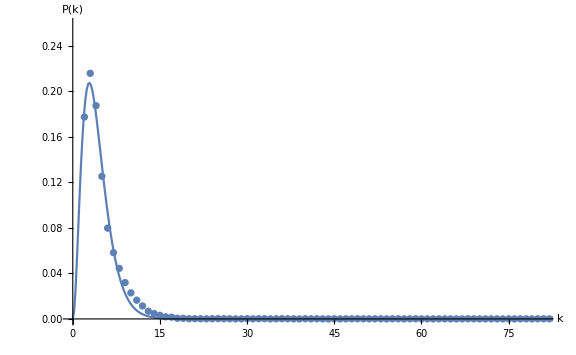

```mathematica
happyOrbitsNVPlot=Show[
ListPlot[happyOrbitsNVDegrees,PlotRange->{{0,81},{0,0.259}},AxesOrigin->{0,0}],
Plot[happyOrbitsNVNlm[x],{x,0,Max[Keys[happyOrbitsNVDegrees]]},PlotRange->{{0,81},{0,0.26}},AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyOrbitsNVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -2.19055 | 0.0848557 | {-2.35854,-2.02255}
c | 0.188599 | 0.00580076 | {0.177115,0.200083}
d | 0.771262 | 0.0224756 | {0.726766,0.815759}

```mathematica
TableForm[Flatten[{"natural visibility",Mean@ VertexDegree[happyOrbitsNVGraph]//N,MeanGraphDistance[happyOrbitsNVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsNVGraph]//N,Mean[happyOrbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}, None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 5.32933 | 100.209 | 0.143567 | 7.1719×10^-6 | -2.19055 ± 0.167994 | 0.188599 ± 0.0114841 | 0.771262 ± 0.0444964

## Horizontal Visibility

```mathematica
happyOrbitsHVLinks=horizontalVisibility[orbits];
```

```mathematica
happyOrbitsHVGraph=Graph[happyOrbitsHVLinks,DirectedEdges->False,GraphLayout->"CircularEmbedding"];
```

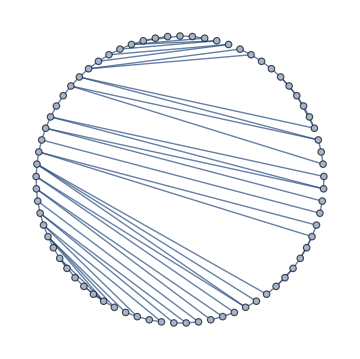

```mathematica
Graph[happyOrbitsHVLinks[[;;100]],DirectedEdges->False,GraphLayout->"CircularEmbedding",ImageSize->Medium]
```

```mathematica
happyOrbitsHVDegrees=Counts[VertexDegree[happyOrbitsHVGraph]]/Length@VertexDegree[happyOrbitsHVGraph]
```

<|1→1/30000,2→4869/10000,3→3757/15000,4→949/6000,5→1111/15000,6→49/2000,7→31/6000,8→7/10000|>

```mathematica
happyOrbitsHVDegrees[1]=.
```

```mathematica
data=Table[{x,happyOrbitsHVDegrees[x]},{x,Keys[happyOrbitsHVDegrees]}];
happyOrbitsHVNlm=NonlinearModelFit[data,c k^-γ E^(-d k),{{γ,2},{c,3},{d,0}},k]
```

FittedModel[1.70584 ⅇ^(-0.765061 k) k^0.391616]

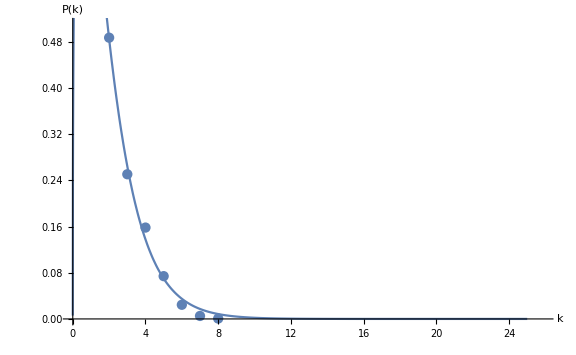

```mathematica
happyOrbitsHVPlot=Show[
ListPlot[happyOrbitsHVDegrees,PlotRange->{{0,25.9},{0,.51}},AxesOrigin->{0,0}],Plot[happyOrbitsHVNlm[x],{x,0,25},PlotRange->Full,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",36, Italic],Style["P(k)", 36,Italic]},LabelStyle->20,ImageSize->Large
]
```

```mathematica
happyOrbitsHVNlm["ParameterConfidenceIntervalTable"]
```

| Estimate | Standard Error | Confidence Interval
γ | -0.391616 | 0.700463 | {-2.33641,1.55318}
c | 1.70584 | 0.16311 | {1.25298,2.15871}
d | 0.765061 | 0.24042 | {0.0975487,1.43257}

```mathematica
TableForm[
Flatten[{"horizontal visibility",Mean@ VertexDegree[happyOrbitsHVGraph]//N,MeanGraphDistance[happyOrbitsHVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsHVGraph]//N,Mean[happyOrbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],TableHeadings->{{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"},None},TableDirections->Row]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
horizontal visibility | 2.917 | 157.073 | 0.255757 | 0.000135784 | -0.391616 ± 1.9448 | 1.70584 ± 0.452865 | 0.765061 ± 0.667512

## Final Results

```mathematica
TableForm[{Flatten[{"natural visibility",Mean@ VertexDegree[happyNVGraph]//N,MeanGraphDistance[happyNVGraph]//N,
GlobalClusteringCoefficient[happyNVGraph]//N,Mean[happyNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],
Flatten[{"horizontal visibility",Mean@ VertexDegree[happyHVGraph]//N,MeanGraphDistance[happyHVGraph]//N,
GlobalClusteringCoefficient[happyHVGraph]//N,Mean[happyHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"natural visibility",Mean@ VertexDegree[happyOrbitsNVGraph]//N,MeanGraphDistance[happyOrbitsNVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsNVGraph]//N,Mean[happyOrbitsNVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsNVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}],Flatten[{"horizontal visibility",Mean@ VertexDegree[happyOrbitsHVGraph]//N,MeanGraphDistance[happyOrbitsHVGraph]//N,
GlobalClusteringCoefficient[happyOrbitsHVGraph]//N,Mean[happyOrbitsHVNlm["FitResiduals"]^2],ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@happyOrbitsHVNlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]},TableHeadings->{None,{"algo","⟨k⟩","⟨l_min⟩","C_c","⟨e^2⟩","γ","C","δ"}}]
```

algo | ⟨k⟩ | ⟨l_min⟩ | C_c | ⟨e^2⟩ | γ | C | δ
natural visibility | 6.60953 | 7.39084 | 0.349324 | 9.56797×10^-6 | -2.24978 ± 0.196962 | 0.0996976 ± 0.00940549 | 0.664207 ± 0.046069
horizontal visibility | 3.5084 | 15.4267 | 0.271018 | 9.76565×10^-6 | 0.713816 ± 0.229998 | 1.33806 ± 0.0648825 | 0.330865 ± 0.0707582
natural visibility | 5.32933 | 100.209 | 0.143567 | 7.1719×10^-6 | -2.19055 ± 0.167994 | 0.188599 ± 0.0114841 | 0.771262 ± 0.0444964
horizontal visibility | 2.917 | 157.073 | 0.255757 | 0.000135784 | -0.391616 ± 1.9448 | 1.70584 ± 0.452865 | 0.765061 ± 0.667512